# Model reduction analysis

## Brusselator

### Bimolecular - only

{X→A,Y→B/A,Z→A^2}

{{-1-4 A-B,A^2,2+B/A},{B,-A^2,-B/A},{2 A,0,-1}}

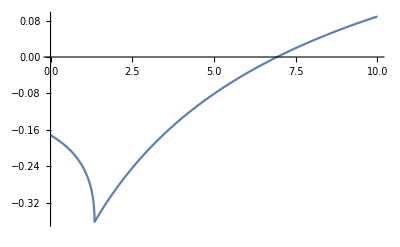

```mathematica
fX1=A-(1+B)X-2 X^2+2Z+Z Y;
fY1=B X-Z Y;
fZ1=X^2-Z;
eq1=Flatten[Solve[{fX1==0,fY1==0,fZ1==0},{X,Y,Z}]]
J1=D[{fX1,fY1,fZ1},{{X,Y,Z}}]/.eq1
Plot[Max[Re[Eigenvalues[N[J1/.{A->1,B->b}]]]],{b,0,10}]
```

{X→A,Y→B/A}

{{-1+B,A^2},{-B,-A^2}}

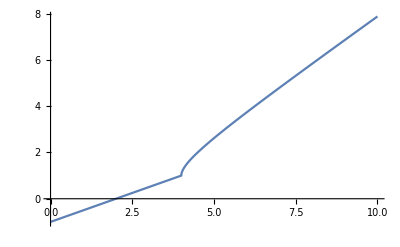

```mathematica
fX2=A-(1+B)X+X^2 Y;
fY2=B X-X^2 Y;
eq2=Flatten[Solve[{fX==0,fY==0},{X,Y}]]
J2=D[{fX2,fY2},{{X,Y}}]/.eq2
Plot[Max[Re[Eigenvalues[N[J2/.{A->1,B->b}]]]],{b,0,10}]
```

## Turing' s example

### 2 species

```mathematica
fx=-k1 x y-2k3 x^2+k4+y (k6 k7 cTot)/(k7+k6 y);
fy=k1 x y+2k3 x^2-k5 y-y (k6 k7 cTot)/(k7+k6 y);
lk6=0;
Table[paras={k1->2,k2->0.2,k3->0.01,k4->0.08,k5->0.04,k6->10^lk6,k7->2,cTot->6};
eq=NSolve[{fx==0,fy==0}/.paras,{x,y}];
J=D[{fx,fy},{{x,y}}]/.paras;
Select[eq,Max[Re[Eigenvalues[J/.#]]]<0&],{lk6,-2,4,0.2}]
```

{{{x→0.0496906,y→2.}},{{x→0.0667827,y→2.}},{{x→0.0934664,y→2.}},{{x→0.134769,y→2.}},{{x→0.197857,y→2.}},{{x→0.2923,y→2.}},{{x→0.429498,y→2.}},{{x→0.620356,y→2.}},{{x→0.870453,y→2.}},{{x→1.1737,y→2.}},{{x→1.50862,y→2.}},{{x→1.84244,y→2.}},{{x→2.1428,y→2.}},{{x→2.38918,y→2.}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}